NDSolve::mxst: Maximum number of 20000 steps reached at the point t == 362.178.

-Graphics-

NDSolve::mxst: Maximum number of 30000 steps reached at the point t == 544.088.

InterpolatingFunction::dmval: Input value {550.265} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {556.549} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {562.832} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 30000 steps reached at the point t == 496.792.

NDSolve::mxst: Maximum number of 30000 steps reached at the point t == 506.915.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

-Graphics-

NDSolve::mxst: Maximum number of 20000 steps reached at the point t == 405.339.

-Graphics-

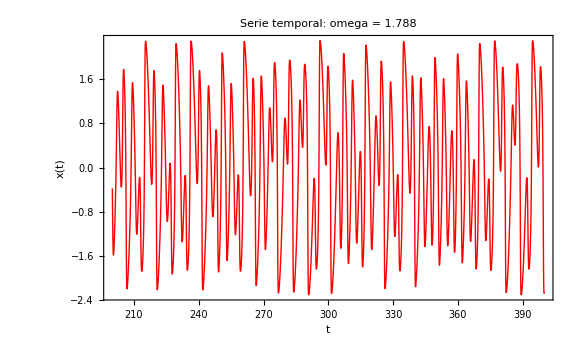

NDSolve::mxst: Maximum number of 30000 steps reached at the point t == 599.155.

NDSolve::mxst: Maximum number of 30000 steps reached at the point t == 600.146.

InterpolatingFunction::dmval: Input value {600.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {602.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {604.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.0460441

NDSolve::mxst: Maximum number of 30000 steps reached at the point t == 544.247.

InterpolatingFunction::dmval: Input value {546.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {548.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {550.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 30000 steps reached at the point t == 492.811.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

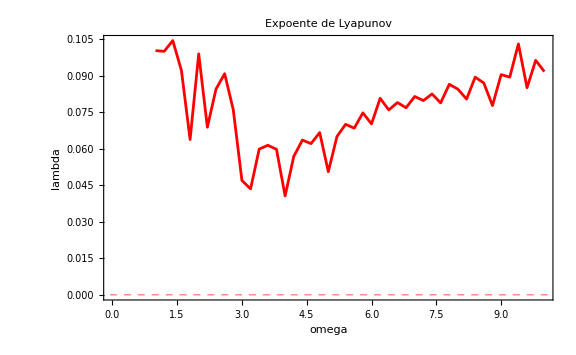

```mathematica
(*PROBLEMA 3:OSCILADOR DE VAN DER POL*)


optam={ImageSize->Large,LabelStyle->"Medium"};

(*Parametros*)
m=1;
k=1;
a=3;
F0=5;

(*------------------------------------------------------------------------*)
(*Item 3.1:Espaco de fase para omega=1*)


sol1=NDSolve[{m*x''[t]+k*x[t]-a*(1-x[t]^2)*x'[t]==F0*Cos[t],x[0]==0,x'[0]==0},{x,x'},{t,0,1300},MaxSteps->20000];

ParametricPlot[Evaluate[{x[t],x'[t]}/. sol1],{t,100,1300},Frame->True,FrameLabel->{"x","v"},PlotLabel->"Espaco de fase: omega = 1",PlotStyle->{Blue,Thick},Evaluate[optam]]

(*------------------------------------------------------------------------*)
(*Item 3.2:Diagrama de bifurcacoes*)


(*Funcao auxiliar para secao de Poincare*)
secaoPoincare[omega_]:=Module[{sol,T,tempos},sol=NDSolve[{m*x''[t]+k*x[t]-a*(1-x[t]^2)*x'[t]==F0*Cos[omega*t],x[0]==0,x'[0]==0},x,{t,0,2000},MaxSteps->30000];
T=2*Pi/omega;
tempos=Range[500,2000,T];
Table[{omega,x[t]/. sol[[1]]},{t,tempos}]]

(*diagrama-intervalo completo*)
pontosBif=Flatten[Table[secaoPoincare[omega],{omega,1.0,10.0,0.05}],1];

ListPlot[pontosBif,PlotStyle->{PointSize[0.002],Red},Frame->True,FrameLabel->{"omega","x"},PlotLabel->"Diagrama de Bifurcacoes",Evaluate[optam]]

(*------------------------------------------------------------------------*)
(*Item 3.3:Analise para omega=1.788*)


sol1788=NDSolve[{m*x''[t]+k*x[t]-a*(1-x[t]^2)*x'[t]==F0*Cos[1.788*t],x[0]==0,x'[0]==0},{x,x'},{t,0,1300},MaxSteps->20000];

(*Espaco de fase*)
ParametricPlot[Evaluate[{x[t],x'[t]}/. sol1788],{t,200,1300},Frame->True,FrameLabel->{"x","v"},PlotLabel->"omega = 1.788",PlotStyle->{Red,Thick},Evaluate[optam]]


Plot[Evaluate[x[t]/. sol1788],{t,200,400},Frame->True,FrameLabel->{"t","x(t)"},PlotLabel->"Serie temporal: omega = 1.788",PlotStyle->{Red,Thick},Evaluate[optam]]

(*------------------------------------------------------------------------*)
(*Item 3.4:Expoente de Lyapunov*)


(*expoente de Lyapunov para um dado omega*)
calcLyap[omega_]:=Module[{sol1,sol2,t1,x1,v1,x2,v2,dist,logd},sol1=NDSolve[{m*x''[t]+k*x[t]-a*(1-x[t]^2)*x'[t]==F0*Cos[omega*t],x[0]==0.4,x'[0]==0.1},{x,x'},{t,0,800},MaxSteps->30000];
sol2=NDSolve[{m*x''[t]+k*x[t]-a*(1-x[t]^2)*x'[t]==F0*Cos[omega*t],x[0]==0.4+10^-8,x'[0]==0.1},{x,x'},{t,0,800},MaxSteps->30000];
t1=Range[100,800,2.];
x1=Table[x[t]/. sol1[[1]],{t,t1}];
v1=Table[x'[t]/. sol1[[1]],{t,t1}];
x2=Table[x[t]/. sol2[[1]],{t,t1}];
v2=Table[x'[t]/. sol2[[1]],{t,t1}];
dist=Sqrt[(x1-x2)^2+(v1-v2)^2];
logd=Log[dist];
Coefficient[Fit[Transpose[{t1,logd}],{1,t},t],t]]

(*Lyapunov em omega=1.788*)
calcLyap[1.788]

(*Grafico lambda(omega)-intervalo estendido*)
dadosLyap=Table[{omega,calcLyap[omega]},{omega,1.0,10.0,0.2}];

ListPlot[dadosLyap,Joined->True,Frame->True,FrameLabel->{"omega","lambda"},PlotLabel->"Expoente de Lyapunov",GridLines->{{},{0}},GridLinesStyle->Directive[Red,Dashed],PlotStyle->Red,Evaluate[optam]]
```